```mathematica
theta0=Pi*x2+(1-h)/2*Sin[2*Pi*x2]
```

π x2+1/2 (1-h) Sin[2 π x2]

```mathematica
theta=(h(2(x2-1/2))+(1-h)(2(x2-1/2))^7+1)Pi/2
```

1/2 π (1+2 h (-1/2+x2)+128 (1-h) (-1/2+x2)^7)

```mathematica
(* Noble *)
theta0plot=theta0//.{h->0.3}
(* Rebecca *)
thetaplot=theta//.{h->0.15}
```

π x2+0.35 Sin[2 π x2]

1/2 π (1+0.3 (-1/2+x2)+108.8 (-1/2+x2)^7)

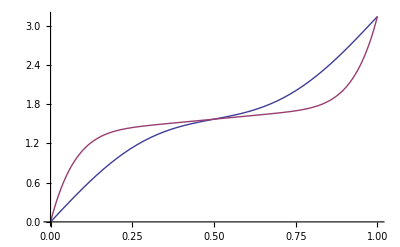

```mathematica
Plot[{theta0plot,thetaplot},{x2,0,1}]
```

```mathematica
D[theta0plot,x2]//.{x2->0.5}
D[thetaplot,x2]//.{x2->0.5}
```

0.942478

0.471239

```mathematica
128./192*6
```

4.